```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../Models/SMS-stop_SMQCD/SMS-stop_SMQCD",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
FR$ClassesTranslation
```

FR$ClassesTranslation

## Top - G - G vertex

generic model {Lorentz} initialized

classes model {../Models/SMS-stop_SMQCD/SMS-stop_SMQCD} initialized

in total: 1 Particles insertion

in total: 1 Particles amplitude

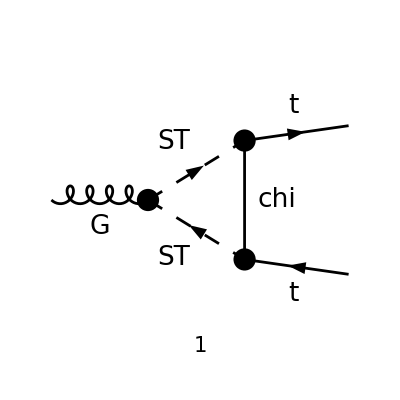

```mathematica
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[1]} -> {F[3],-F[3]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1]}];
(* Set Truncated->True to remove external fields  *)
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->False,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings,ChangeDimension->D];
nonZero={};
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	If[!M==={0},AppendTo[nonZero,n]];
];
goodDiags=DiagramExtract[allDiags,nonZero];
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,LorentzIndexNames-> {μ,ν},SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 1 Particles amplitude

(2 √π √aS T_Col2Col3^Glu1 (p1+p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(mChi+γ·(p1-q)).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((q-p1)^2-mChi^2).((-p1-p2+q)^2-mST^2))

```mathematica
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

-(2 √π √aS yDM^2 T_Col2Col3^Glu1 (p1^μ+p2^μ-2 q^μ) ((γ·p1).(γ̄)^6-(γ·q).(γ̄)^6))/((q^2-mST^2).((p1-q)^2-mChi^2).((p1+p2-q)^2-mST^2))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify)
```

-2 ⅈ π^(5/2) √aS yDM^2 T_Col2Col3^Glu1 (2 γ^μ.(γ̄)^6 C_00(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+(p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 p1^μ (γ·p1).(γ̄)^6 C_11(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-(p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_2(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 p2^μ (γ·p2).(γ̄)^6 C_22(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2))

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampD=Simplify[ ampC]
```

-2 ⅈ π^(5/2) √aS yDM^2 T_Col2Col3^Glu1 (2 γ^μ.(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+(p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)-(p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 p1^μ (γ·p1).(γ̄)^6 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 p2^μ (γ·p2).(γ̄)^6 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)-2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2))

```mathematica
ampE = Expand[Collect[Simplify[( ampD)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},foo]]/.foo->FullSimplify
```

-2 ⅈ π^2 GS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+ⅈ π^2 GS yDM^2 p2^μ T_Col2Col3^Glu1 ((γ·p1).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2))-(γ·p2).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)))-ⅈ π^2 GS yDM^2 p1^μ T_Col2Col3^Glu1 ((γ·p1).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2))-(γ·p2).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)))

```mathematica
UVpart = DiracSimplify[PaXEvaluateUV[ampC,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)]]
```

-(ⅈ √aS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(16 π^(3/2) ε_UV)

## Top-Top - G - G vertex

generic model {Lorentz} initialized

classes model {../Models/SMS-stop_SMQCD/SMS-stop_SMQCD} initialized

in total: 3 Particles insertions

in total: 3 Particles amplitudes

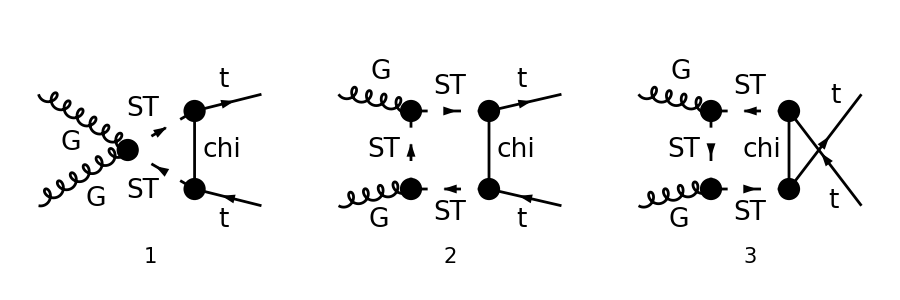

```mathematica
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGTT =  { V[1],V[1]} -> {F[3],-F[3]};
allDiags = InsertFields[tops,processGGTT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],F[3]}];
(* Set Truncated->True to remove external fields  *)
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->False,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings,ChangeDimension->D];
nonZero={};
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	If[!M==={0},AppendTo[nonZero,n]];
];
goodDiags=DiagramExtract[allDiags,nonZero];
Paint[goodDiags,ColumnsXRows->{3,1},ImageSize->{ 900,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,LorentzIndexNames-> {μ,ν},SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 3 Particles amplitudes

(4 π aS (-k2-2 q)^ν T_Col3Col5^Glu2 T_Col5Col4^Glu1 (-k2+p1+p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(γ·(-k2+p1-q)+mChi).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))+(4 π aS (-k2-2 q)^ν T_Col3Col5^Glu1 T_Col5Col4^Glu2 (-k2+p1+p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(γ·(k2-p2+q)+mChi).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))-(4 π aS g^μν ((T^Glu1 T^Glu2)_Col3Col4+(T^Glu2 T^Glu1)_Col3Col4) (-ⅈ yDM (γ̄)^7).(mChi-γ·q).(-ⅈ yDM (γ̄)^6))/((q^2-mChi^2).((p1+q)^2-mST^2).((q-p2)^2-mST^2))

## For this coupling we can assume on-shell gluons and tops

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[k1,k1]=0;
ScalarProduct[k2,k2]=0;
ScalarProduct[k1,k2]=s/2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

Also assume the gluons are have transverse polarization (on-shell gluons)

```mathematica
PT =1/2( MTD[μ,ν]-FVD[k1,ν]FVD[k2,μ]/ScalarProduct[k1,k2]);
```

```mathematica
ampB = Contract[PT SUNSimplify[FCTraceFactor[DiracSimplify[ampA]]]]//Simplify
```

-1/s 2 π aS yDM^2 ((γ·q).(γ̄)^6 (((D-1) s ((T^Glu1 T^Glu2)_Col3Col4+(T^Glu2 T^Glu1)_Col3Col4))/((q^2-mChi^2).((p1+q)^2-mST^2).((p2-q)^2-mST^2))+2 (2 (k1·q) (k2·p1+k2·p2-2 (k2·q))+s (k2·q-p1·q-p2·q+2 q^2)) (((T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))-((T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))))+2 (2 (k1·q) (k2·p1+k2·p2-2 (k2·q))+s (k2·q-p1·q-p2·q+2 q^2)) (-((γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))+((γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))+(γ·k2).(γ̄)^6 (((T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))-((T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2)))))

```mathematica
ampC = TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify
```

1/s 2 ⅈ aS π^3 yDM^2 (s C_0(MT^2,0,MT^2-2 (k2·p2),mChi^2,mST^2,mST^2) (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col3Col4+(4 mST^2-s) s D_0(MT^2,MT^2,0,s-2 (k2·p1)-2 (k2·p2),s,MT^2-2 (k2·p2),mST^2,mChi^2,mST^2,mST^2) (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col3Col4-2 C_0(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (γ·p1).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) (T^Glu1 T^Glu2)_Col3Col4+s (γ·k2).(γ̄)^6 C_1(0,MT^2-2 (k2·p2),MT^2,mST^2,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col3Col4-2 (γ·p1).(γ̄)^6 (s-4 (k1·p1)-2 (k1·p2)) C_1(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-s ((s-4 mST^2) (γ·k2).(γ̄)^6+2 (γ·p2).(γ̄)^6 (k2·p1+k2·p2)) D_1(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+s (γ·p2).(γ̄)^6 C_2(0,MT^2-2 (k2·p2),MT^2,mST^2,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col3Col4-2 ((γ·p1).(γ̄)^6+(-(γ·(k2-p1-p2))).(γ̄)^6) (s-2 (k1·p1)-2 (k1·p2)) C_2(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+(γ·p2).(γ̄)^6 ((4 mST^2-s) s-4 (k1·p2) (k2·p1+k2·p2)) D_2(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-((4 mST^2-s) s (-(γ·(p1+p2))).(γ̄)^6+4 (γ·p2).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2)) D_3(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (γ·k1).(γ̄)^6 C_00(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·k1).(γ̄)^6 (k2·p1+k2·p2) D_00(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (γ·p1).(γ̄)^6 (k1·p1) C_11(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 s (γ·k2).(γ̄)^6 (k2·p1+k2·p2) D_11(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 ((γ·p1).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2))-2 (-(γ·(k2-p1-p2))).(γ̄)^6 (k1·p1)) C_12(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 (s (γ·p2).(γ̄)^6+2 (γ·k2).(γ̄)^6 (k1·p2)) (k2·p1+k2·p2) D_12(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 (s (-(γ·(p1+p2))).(γ̄)^6-2 (γ·k2).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_13(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 (-(γ·(k2-p1-p2))).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_22(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·p2).(γ̄)^6 (k1·p2) (k2·p1+k2·p2) D_22(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 ((γ·p2).(γ̄)^6 (k1·p1+k1·p2)-(-(γ·(p1+p2))).(γ̄)^6 (k1·p2)) (k2·p1+k2·p2) D_23(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (-(γ·(p1+p2))).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2) D_33(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·k1).(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)-4 ((γ·p1).(γ̄)^6 (k1·p1)+(γ·p2).(γ̄)^6 (k1·p2)) C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)+4 ((γ·p2).(γ̄)^6 (k1·p1)+(γ·p1).(γ̄)^6 (k1·p2)) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)-s C_0(MT^2,0,MT^2-2 (k2·p1),mChi^2,mST^2,mST^2) (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col3Col4-(4 mST^2-s) s D_0(MT^2,MT^2,0,s-2 (k2·p1)-2 (k2·p2),s,MT^2-2 (k2·p1),mST^2,mChi^2,mST^2,mST^2) (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col3Col4+2 C_0(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (γ·p2).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) (T^Glu2 T^Glu1)_Col3Col4-s (γ·k2).(γ̄)^6 C_1(0,MT^2-2 (k2·p1),MT^2,mST^2,mST^2,mChi^2) (T^Glu2 T^Glu1)_Col3Col4+2 (γ·p2).(γ̄)^6 (s-2 (k1·p1)-4 (k1·p2)) C_1(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+s ((s-4 mST^2) (γ·k2).(γ̄)^6+2 (γ·p1).(γ̄)^6 (k2·p1+k2·p2)) D_1(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-s (γ·p1).(γ̄)^6 C_2(0,MT^2-2 (k2·p1),MT^2,mST^2,mST^2,mChi^2) (T^Glu2 T^Glu1)_Col3Col4+2 ((-(γ·(k2-p1-p2))).(γ̄)^6+(γ·p2).(γ̄)^6) (s-2 (k1·p1)-2 (k1·p2)) C_2(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-(γ·p1).(γ̄)^6 ((4 mST^2-s) s-4 (k1·p1) (k2·p1+k2·p2)) D_2(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+((4 mST^2-s) s (-(γ·(p1+p2))).(γ̄)^6+4 (γ·p1).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2)) D_3(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 (γ·k1).(γ̄)^6 C_00(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·k1).(γ̄)^6 (k2·p1+k2·p2) D_00(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 (γ·p2).(γ̄)^6 (k1·p2) C_11(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 s (γ·k2).(γ̄)^6 (k2·p1+k2·p2) D_11(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 ((γ·p2).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2))-2 (-(γ·(k2-p1-p2))).(γ̄)^6 (k1·p2)) C_12(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 (s (γ·p1).(γ̄)^6+2 (γ·k2).(γ̄)^6 (k1·p1)) (k2·p1+k2·p2) D_12(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 (s (-(γ·(p1+p2))).(γ̄)^6-2 (γ·k2).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_13(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 (-(γ·(k2-p1-p2))).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_22(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·p1).(γ̄)^6 (k1·p1) (k2·p1+k2·p2) D_22(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 ((γ·p1).(γ̄)^6 (k1·p1+k1·p2)-(-(γ·(p1+p2))).(γ̄)^6 (k1·p1)) (k2·p1+k2·p2) D_23(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 (-(γ·(p1+p2))).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2) D_33(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6) C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((4 (k1·p2)-(D-2) s) (T^Glu1 T^Glu2)_Col3Col4+(4 (k1·p1)-(D-2) s) (T^Glu2 T^Glu1)_Col3Col4))

```mathematica
SUNSimplify[%]
```

1/s 2 ⅈ aS π^3 yDM^2 (s C_0(MT^2,0,MT^2-2 (k2·p2),mChi^2,mST^2,mST^2) (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col3Col4+(4 mST^2-s) s D_0(MT^2,MT^2,0,s-2 (k2·p1)-2 (k2·p2),s,MT^2-2 (k2·p2),mST^2,mChi^2,mST^2,mST^2) (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col3Col4-2 C_0(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (γ·p1).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) (T^Glu1 T^Glu2)_Col3Col4+s (γ·k2).(γ̄)^6 C_1(0,MT^2-2 (k2·p2),MT^2,mST^2,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col3Col4+((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6) (4 (k1·p2)-(D-2) s) C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 (γ·p1).(γ̄)^6 (s-4 (k1·p1)-2 (k1·p2)) C_1(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-s ((s-4 mST^2) (γ·k2).(γ̄)^6+2 (γ·p2).(γ̄)^6 (k2·p1+k2·p2)) D_1(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+s (γ·p2).(γ̄)^6 C_2(0,MT^2-2 (k2·p2),MT^2,mST^2,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col3Col4-2 (γ·p1-γ·(k2-p1-p2)).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_2(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+(γ·p2).(γ̄)^6 ((4 mST^2-s) s-4 (k1·p2) (k2·p1+k2·p2)) D_2(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-(4 (γ·p2).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2)-(4 mST^2-s) s (γ·(p1+p2)).(γ̄)^6) D_3(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·k1).(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (γ·k1).(γ̄)^6 C_00(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·k1).(γ̄)^6 (k2·p1+k2·p2) D_00(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 ((γ·p1).(γ̄)^6 (k1·p1)+(γ·p2).(γ̄)^6 (k1·p2)) C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (γ·p1).(γ̄)^6 (k1·p1) C_11(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 s (γ·k2).(γ̄)^6 (k2·p1+k2·p2) D_11(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 ((γ·p2).(γ̄)^6 (k1·p1)+(γ·p1).(γ̄)^6 (k1·p2)) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 (2 (γ·(k2-p1-p2)).(γ̄)^6 (k1·p1)+(γ·p1).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2))) C_12(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 (s (γ·p2).(γ̄)^6+2 (γ·k2).(γ̄)^6 (k1·p2)) (k2·p1+k2·p2) D_12(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 (-s (γ·(p1+p2)).(γ̄)^6-2 (γ·k2).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_13(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 (γ·(k2-p1-p2)).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_22(MT^2,MT^2-2 (k2·p2),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·p2).(γ̄)^6 (k1·p2) (k2·p1+k2·p2) D_22(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 ((γ·(p1+p2)).(γ̄)^6 (k1·p2)+(γ·p2).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_23(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 (γ·(p1+p2)).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2) D_33(0,MT^2-2 (k2·p2),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-s C_0(MT^2,0,MT^2-2 (k2·p1),mChi^2,mST^2,mST^2) (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col3Col4-(4 mST^2-s) s D_0(MT^2,MT^2,0,s-2 (k2·p1)-2 (k2·p2),s,MT^2-2 (k2·p1),mST^2,mChi^2,mST^2,mST^2) (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col3Col4+2 C_0(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (γ·p2).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) (T^Glu2 T^Glu1)_Col3Col4-s (γ·k2).(γ̄)^6 C_1(0,MT^2-2 (k2·p1),MT^2,mST^2,mST^2,mChi^2) (T^Glu2 T^Glu1)_Col3Col4+((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6) (4 (k1·p1)-(D-2) s) C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 (γ·p2).(γ̄)^6 (s-2 (k1·p1)-4 (k1·p2)) C_1(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+s ((s-4 mST^2) (γ·k2).(γ̄)^6+2 (γ·p1).(γ̄)^6 (k2·p1+k2·p2)) D_1(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-s (γ·p1).(γ̄)^6 C_2(0,MT^2-2 (k2·p1),MT^2,mST^2,mST^2,mChi^2) (T^Glu2 T^Glu1)_Col3Col4+2 (γ·p2-γ·(k2-p1-p2)).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_2(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-(γ·p1).(γ̄)^6 ((4 mST^2-s) s-4 (k1·p1) (k2·p1+k2·p2)) D_2(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+(4 (γ·p1).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2)-(4 mST^2-s) s (γ·(p1+p2)).(γ̄)^6) D_3(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·k1).(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 (γ·k1).(γ̄)^6 C_00(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·k1).(γ̄)^6 (k2·p1+k2·p2) D_00(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 ((γ·p1).(γ̄)^6 (k1·p1)+(γ·p2).(γ̄)^6 (k1·p2)) C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 (γ·p2).(γ̄)^6 (k1·p2) C_11(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 s (γ·k2).(γ̄)^6 (k2·p1+k2·p2) D_11(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 ((γ·p2).(γ̄)^6 (k1·p1)+(γ·p1).(γ̄)^6 (k1·p2)) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 ((γ·p2).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2))+2 (γ·(k2-p1-p2)).(γ̄)^6 (k1·p2)) C_12(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 (s (γ·p1).(γ̄)^6+2 (γ·k2).(γ̄)^6 (k1·p1)) (k2·p1+k2·p2) D_12(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 (-s (γ·(p1+p2)).(γ̄)^6-2 (γ·k2).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_13(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 (γ·(k2-p1-p2)).(γ̄)^6 (s-2 (k1·p1)-2 (k1·p2)) C_22(MT^2,MT^2-2 (k2·p1),s-2 (k2·p1)-2 (k2·p2),mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·p1).(γ̄)^6 (k1·p1) (k2·p1+k2·p2) D_22(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 ((γ·(p1+p2)).(γ̄)^6 (k1·p1)+(γ·p1).(γ̄)^6 (k1·p1+k1·p2)) (k2·p1+k2·p2) D_23(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+4 (γ·(p1+p2)).(γ̄)^6 (k1·p1+k1·p2) (k2·p1+k2·p2) D_33(0,MT^2-2 (k2·p1),MT^2,s,MT^2,s-2 (k2·p1)-2 (k2·p2),mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4)

```mathematica
UVpart = DiracSimplify[PaXEvaluateUV[ampC]]
```

0